-Graphics3D-

-Graphics3D-

-Graphics3D-

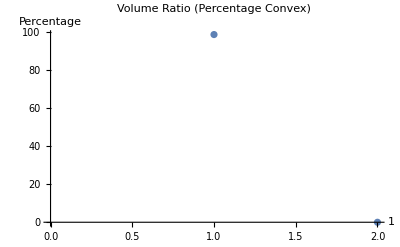

{98.5704,0.}

69.6998

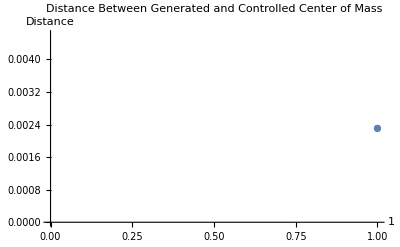

{0.00230607}

StandardDeviation::shlen: The argument {0.00230607} should have at least two elements.

StandardDeviation[{0.00230607}]

-Graphics3D-

5

```mathematica
Trials=1; (*Number of trials desired*)
Beamradius=.5; (*Beamradius currently 5mm*)
A=π*Beamradius^2;
α=1; (*α is of the order 0.6-1.4 cm^-1*)
r=30; (*Radius of sphere in units of cm*)
Highest=r; (*Initializes the upper bound of the object*)
Lowest=-r; (*Initializes the lower bound of the object*)
SignalDecay=A*ⅇ^(-α*x);


TotalS=10000; (*Approximately the number of data points*)
NDimensions=3; (*3-Dimensional object - Sphere*)
Start=1;
Restart=1;
Finish=1;
SurfacePoints=Table[0,{i,TotalS},{j,NDimensions}];
NewSurface=Table[0,{i,TotalS},{j,NDimensions}]; (*Random points on the surface of the sphere*)
VPTable=Table[0,{i,Trials+1}];
CMTable=Table[0,{i,Trials}];
(*SphereVolume=4/3 π*r^3*) (*Unneeded as the volume of the control sphere is calculated with the convex hull*)

(*This loop generates points on the surface of the control sphere.*)
For[i=1,i≤ TotalS,i++,

xrand=RandomReal[{-1,1}];
yrand=RandomReal[{-1,1}];
zrand=RandomReal[{-1,1}];
x=r*xrand/(√(xrand^2+yrand^2+zrand^2));
y=r*yrand/(√(xrand^2+yrand^2+zrand^2));
z=r*zrand/(√(xrand^2+yrand^2+zrand^2));
SurfacePoints[[i,1]]=x;
SurfacePoints[[i,2]]=y;
SurfacePoints[[i,3]]=z;

];  (*For loop generates a number of surface points corresponding to TotalS*)

SurfaceModel=ConvexHullMesh[SurfacePoints]; (*Creates a mesh for the control sphere*)
SphereVolume=RegionMeasure[SurfaceModel]; (*Finds the volume of the control sphere*)
SurfaceCM=RegionCentroid[SurfaceModel]; (*Finds the center of mass for the control sphere*)

(*This For loop runs as many times as Trials specify*)
(*The Loop begins at 2 so that the first trial may be 0 to put the percentages into scale*)
For[i=1,i≤Trials,i++,

(*The For loop that generates new points between the center of mass and the corresponding j, a surface point*)
For[j=1,j≤TotalS,j++,

Start=Restart;

(* This While loop has generates a t-value for a x-value that falls under the curve*)
While[Start≤Finish,
x=RandomReal[{0,r}];
y=RandomReal[];

(*If loop tests to find x-values that falls under the curve and scales it to t-values*)
(*Since it is a line there is no differentiation between sphereical and cartesian coordinates*)
If[y<A*ⅇ^(-α*x),

(*This t-value ranges in values from [0,1]. At t=0, the point is located on the surface and when t=1 the point is located at the center of mass*)
t=1/r*x;
Start++;]
];

(*This first picks a line from the center of mass to a surface point, it then generates an x, y, and z; [[j,1]], [[j,1]], and [[j,3]] respectively*)
NewSurface[[j,1]]=SurfaceCM[[1]]*t+SurfacePoints[[j,1]]*(1-t);
NewSurface[[j,2]]=SurfaceCM[[2]]*t+SurfacePoints[[j,2]]*(1-t);
NewSurface[[j,3]]=SurfaceCM[[3]]*t+SurfacePoints[[j,3]]*(1-t);]; 

(*For each trial the convex hull mesh, volume, and center of mass are calculated*)
GeneratedSphere=ConvexHullMesh[NewSurface];
GeneratedVolume=RegionMeasure[GeneratedSphere];
GeneratedCM=RegionCentroid[GeneratedSphere];

(*This finds the ratio of the generated volume to the actual volume*)
VolumePercentage=GeneratedVolume/SphereVolume*100;
(*The corresponding volume percentages are placed in a table for display*)
VPTable[[i]]=VolumePercentage;

(*The last table finds the distance between the center of masses*)
CMTable[[i]]=EuclideanDistance[SurfaceCM,GeneratedCM];
];

(*This is the first image and it shows the general locations of the points*)
ListPointPlot3D[NewSurface,BoxRatios->Automatic]

(*Displays the convex hull of the model in which all points are on the surface*)
SurfaceModel

(*Displays the generated model*)
GeneratedSphere

(*Plots the volume ratio percentage, though the values are slightly off as the first value is set to 0 so that the values can be put in perspective*)
ListPlot[VPTable,AxesLabel->{Trials,Percentage},AxesStyle->{Black,15},PlotLabel->"Volume Ratio (Percentage Convex)",LabelStyle->Directive[Bold]]

(*Finds the average of the volume percentages*)
MovingAverage[VPTable,Trials]

(*Finds the standard deviation between the volume percentages*)
StandardDeviation[VPTable]

(*Plots the distances between the center of masses, note that this should be compared to the radius to understand the scale*)
ListPlot[CMTable,AxesLabel->{Trials,Distance},AxesStyle->{Black,15},PlotLabel->"Distance Between Generated and Controlled Center of Mass",LabelStyle->Directive[Bold]]

(*Finds the average distance between the center of masses*)
MovingAverage[CMTable,Trials]

(*Finds the standard deviation for the center of masses*)
StandardDeviation[CMTable]

(*TOMOGRAPHIC SLICING*)
(*This section begins the creating of tomographic slices*)
(*Specifies the increments and the distance of an interval*)
Inc=.1;

(*Initializes the bottom and top layers of the interval*)
bot=0;
top =bot+Inc;

(*Calculates the number of slices of tomographic data based on the total distance and the value of the increments*)
NumLevels=(Highest-Lowest)/Inc;

(*This halfway value allows for the plotting of a slice on the xy-plane, z=0*)
Halfway=NumLevels/2+1;

(*Creates a list of tables for the tomographic slices*)
(*One problem is that the points that don't fall in the interval will end up with the noise point {0,0,0}*)
Levels=Table[0,{i,1,NumLevels},{j,1,TotalS},{k,NDimensions}];

(*This For loop begins by picking and interval with bot as the bottom bound and top as the upper bound*)
For[k=1,k≤NumLevels,k++,

bot=Lowest+(k-1)*Inc;
top=Lowest+(k)*Inc;

(*This next loop goes through the rows of the 10,000 NewSurface points we have generated and makes a decision, next comments for specifications*)
For[m=1,m≤TotalS,m++,

(*This If statement checks to see if the z-coordinate of each coordinate pair falls within the interval of bot and top*)
If[bot≤NewSurface[[m,3]]≤top,

(*If the statement evaluates to true, x-coordinate and y-coordinate are left alone and the z-coordinate is flattened to the value specified as bot*)
(*Also the point is saved within the level so that we can output a slice*)
NewSurface[[m,3]]=bot;
Levels[[k,m]]=NewSurface[[m]];
];
];
];

(*This plot displays the slice located with the bottom bound at 0 and the top bound 1 increment above*)
(*This is a convenient slice as all the points lie on the same slice though {0,0,0} is still most likely noise*)
ListPointPlot3D[Levels[[Halfway]],BoxRatios->Automatic]
*)
```